# An example demonstraiting different optimal points using simple and improved significance estimate

## Kyle Cranmer, July 8, 2014

Here’s a plot of an example background (blue) and signal (red) distribution. The goal is to optimize the cut on x.

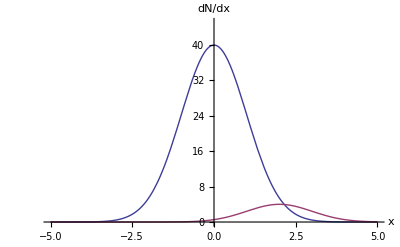

```mathematica
Plot[{100*PDF[NormalDistribution[0,1],x]
,10*PDF[NormalDistribution[2,1],x]},{x,-5,5}, PlotRange->{0,45},AxesLabel->{x,dN/dx}]
```

Define number of signal and background satisfying cut.

```mathematica
s[cut_] := 10*(1-CDF[NormalDistribution[1,1],cut])
```

```mathematica
b[cut_] := 100*(1-CDF[NormalDistribution[0,1],cut])
```

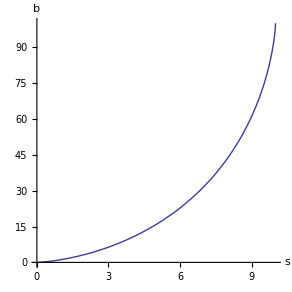

```mathematica
ParametricPlot[{s[cut],b[cut]},{cut,-5,5},AxesLabel->{s,b},  AspectRatio->1]
```

Define simple and improved significance estimates, find cut value that maximizes them.

```mathematica
Simple[S_, B_, sigma_]:=S/Sqrt[B+sigma^2]
```

```mathematica
ZA[S_,B_,sigma_]:=Sqrt[2 ((S+B) Log[((S+B) (B+sigma^2))/(B^2 + (S+B) sigma^2)]- (B^2/sigma^2) Log[1+(S sigma^2)/(B (B+sigma^2))])]
```

```mathematica
Maximize[N[Simple[s[x],b[x],1]],x]
```

{1.23101,{x→0.710368}}

```mathematica
Maximize[N[ZA[s[x],b[x],1]],x]
```

{1.18309,{x→0.597082}}

```mathematica
SimplePoint={N[s[0.71]], N[b[0.71]]}
```

{6.14092,23.8852}

```mathematica
ZAPoint={N[s[0.597]], N[b[0.597]]}
```

{6.56526,27.5254}

Make a plot showing  significance estimates peaking in different places

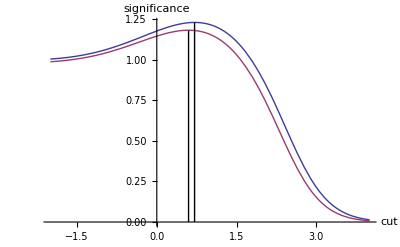

```mathematica
line1=Line[{{0.71,0},{0.71,1.23}}];
line2=Line[{{0.597,0},{0.597,1.18}}];
Plot[{Simple[s[cut], b[cut],1],
ZA[s[cut], b[cut],1]},
{cut,-2,4},Epilog->{line1,line2}, AxesLabel->{cut,significance}]
```

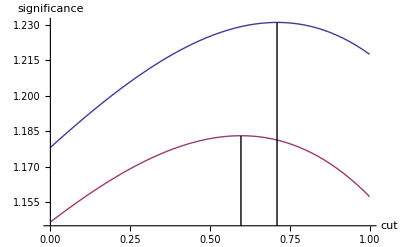

```mathematica
line1=Line[{{0.71,0},{0.71,1.231}}];
line2=Line[{{0.597,0},{0.597,1.183}}];
Plot[{Simple[s[cut], b[cut],1],
ZA[s[cut], b[cut],1]},
{cut,0,1},Epilog->{line1,line2}, AxesLabel->{cut,significance}]
```

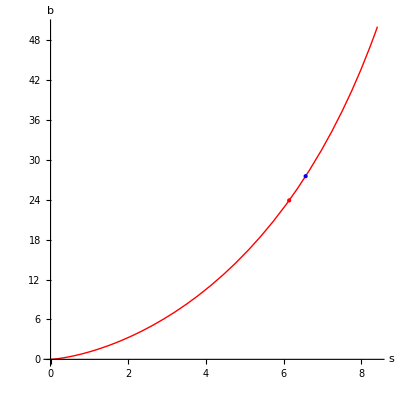

```mathematica
plot = ParametricPlot[{s[cut],b[cut]},{cut,0,4},PlotStyle->{Red},AspectRatio->1,AxesLabel->{s,b},Epilog->{PointSize[Large],Red,Point[{SimplePoint}],Blue,Point[ZAPoint]}]
```

Make contour plots of two significance estimates

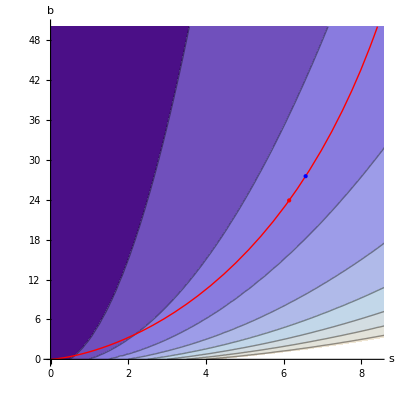

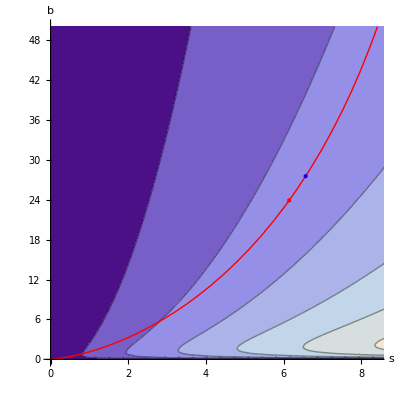

```mathematica
Show[plot,ContourPlot[{Simple[S,B,1]}, {S,0,10},{B,0,50}],plot]
Show[plot,ContourPlot[{ZA[S,B,1]}, {S,0,10},{B,0,50},Epilog->{PointSize[Large],Red,Point[ZAPoint]}],plot]
```